```mathematica
Quit[]
```

## RunMe()

```mathematica
AppendTo[$Path, NotebookDirectory[]];
```

```mathematica
<<USMEFT`
```

## Zprime benchmarks points

```mathematica
benchmarksZp = {
(* 4 TeV *)
<|"MXX" -> 4, "β" -> 0.3|>,
<|"MXX" -> 4, "β" -> 0.5|>,
<|"MXX" -> 4, "β" -> 0.8|>,
<|"MXX" -> 4, "β" -> 1.0|>,
<|"MXX" -> 4, "β" -> 1.2|>,
(* 5 TeV *)
<|"MXX" -> 5, "β" -> 0.3|>,
<|"MXX" -> 5, "β" -> 0.5|>,
<|"MXX" -> 5, "β" -> 0.8|>,
<|"MXX" -> 5, "β" -> 1.0|>,
<|"MXX" -> 5, "β" -> 1.2|>,
<|"MXX" -> 5, "β" -> 1.5|>,
(* 6 TeV *)
<|"MXX" -> 6, "β" -> 0.3|>,
<|"MXX" -> 6, "β" -> 0.5|>,
<|"MXX" -> 6, "β" -> 0.8|>,
<|"MXX" -> 6, "β" -> 1.0|>,
<|"MXX" -> 6, "β" -> 1.2|>,
<|"MXX" -> 6, "β" -> 1.5|>,
(* 7 TeV *)
<|"MXX" -> 7, "β" -> 0.3|>,
<|"MXX" -> 7, "β" -> 0.5|>,
<|"MXX" -> 7, "β" -> 0.8|>,
<|"MXX" -> 7, "β" -> 1.0|>,
<|"MXX" -> 7, "β" -> 1.2|>,
<|"MXX" -> 7, "β" -> 1.5|>,
<|"MXX" -> 7, "β" -> 2.0|>,
(* 8 TeV *)
<|"MXX" -> 8, "β" -> 0.3|>,
<|"MXX" -> 8, "β" -> 0.5|>,
<|"MXX" -> 8, "β" -> 0.8|>,
<|"MXX" -> 8, "β" -> 1.0|>,
<|"MXX" -> 8, "β" -> 1.2|>,
<|"MXX" -> 8, "β" -> 1.5|>,
<|"MXX" -> 8, "β" -> 2.0|>
};
```

## Matching relations

### Matching of the four-fermion operators

```mathematica
EWparam = {
g1 -> SMParam["ee"]/ SMParam["cθ"],
g2 -> SMParam["ee"]/ SMParam["sθ"],
vev -> SMParam["vev"],
Λ -> GetEFTScale[]
}
```

{g1→0.355976,g2→0.649553,vev→246.22,Λ→1000}

```mathematica
matchingZp = {
WC["2JB"] -> -0.5 β^2 / MXX^2,
WC["2ψ4D2"] -> -0.5 β^2/MXX^4,
WC[name:Except["2JB"|"2ψ4D2"]] :> 0
};
```

## Loads benchmark and return χ2 function

```mathematica
(* !!! OrderEFT = 2 OR 4 & OpDim = 6 OR 8 !!! *)
```

```mathematica
Buildχ2[βparam_, MXXparam_,  OrderEFT_, OpDim_, matching_] := Module[
{
χ2ew, χ2lhc
},
(* Loads the pseudo-data for the NCDY channel *)
LoadZprimeBenchmark[βvalue -> βparam, mxxvalue -> MXXparam];
(* Updates the EWPO using the current benchmark points *)
(*LoadZprimeBenchmarkEW[matchingZp, {β-> βparam, MXX -> MXXparam}, EFTOrder -> OrderEFT, OperatorDimension -> OpDim];*)
(* Builds χ2 *)
(*χ2ew = χ2EWPO[EFTOrder-> OrderEFT, OperatorDimension-> OpDim];*)
χ2lhc = χ2LHC[EFTOrder-> OrderEFT, OperatorDimension-> OpDim];

Return [χ2lhc]
]
```

```mathematica
LoadZprimeBenchmark[βvalue->1, mxxvalue->6]
```

```mathematica
χ2d6 = χ2LHC[ObservablesList-> {"NCDY"} ,EFTOrder->2, OperatorDimension->6, WilsonCoefficients->{WC["2JB"], WC["BW"], WC["ϕ,1"]}]//Simplify
```

61.8104+30409. (c_(2JB))^2+32.3857 (c_BW)^2+c_(2JB) (1487.13-1264.58 c_BW-506.741 c_(ϕ,1))-14.9621 c_(ϕ,1)+5.25133 (c_(ϕ,1))^2+c_BW (-37.2365+26.0779 c_(ϕ,1))

```mathematica
Minimize[{χ2d6/.matchingZp/.MXX->4, β >0}, β]
```

{43.5862,{β→0.882501}}

```mathematica
χ2d6sq = χ2LHC[ObservablesList-> {"NCDY"} ,EFTOrder->4, OperatorDimension->6, WilsonCoefficients->{WC["2JB"], WC["BW"], WC["ϕ,1"]}]//Simplify
```

61.8104+965364. (c_(2JB))^4+1.35505 (c_BW)^4-14.9621 c_(ϕ,1)+6.22559 (c_(ϕ,1))^2-0.677483 (c_(ϕ,1))^3+0.0218556 (c_(ϕ,1))^4+(c_BW)^3 (-13.2463+1.46215 c_(ϕ,1))+(c_(2JB))^3 (308853.+47629. c_BW+7329.78 c_(ϕ,1))+(c_BW)^2 (40.0948-12.4809 c_(ϕ,1)+0.738615 (c_(ϕ,1))^2)+c_BW (-37.2365+30.2339 c_(ϕ,1)-4.56038 (c_(ϕ,1))^2+0.185695 (c_(ϕ,1))^3)+(c_(2JB))^2 (35708.7+1585.03 (c_BW)^2-177.15 c_(ϕ,1)+124.02 (c_(ϕ,1))^2+c_BW (5349.27+682.588 c_(ϕ,1)))+c_(2JB) (1487.13+41.0876 (c_BW)^3-471.231 c_(ϕ,1)+20.8494 (c_(ϕ,1))^2+0.795592 (c_(ϕ,1))^3+(c_BW)^2 (63.4474+28.4294 c_(ϕ,1))+c_BW (-1032.31+31.0689 c_(ϕ,1)+8.58041 (c_(ϕ,1))^2))

```mathematica
Minimize[{χ2d6sq/.matchingZp/.MXX->4, β >0}, β]
```

{41.6761,{β→1.02038}}

```mathematica
χ2d8 = χ2LHC[ObservablesList-> {"NCDY"} ,EFTOrder->4, OperatorDimension->8, WilsonCoefficients->{WC["2JB"], WC["2ψ4D2"], WC["BW"], WC["ϕ,1"]}]//Simplify
```

61.8104+965364. (c_(2JB))^4+1.05742×10^6 (c_(ψ^4D^2)^(2))^2-37.2365 c_BW+40.0948 (c_BW)^2-13.2463 (c_BW)^3+1.35505 (c_BW)^4-14.9621 c_(ϕ,1)+30.2339 c_BW c_(ϕ,1)-12.4809 (c_BW)^2 c_(ϕ,1)+1.46215 (c_BW)^3 c_(ϕ,1)+6.22559 (c_(ϕ,1))^2-4.56038 c_BW (c_(ϕ,1))^2+0.738615 (c_BW)^2 (c_(ϕ,1))^2-0.677483 (c_(ϕ,1))^3+0.185695 c_BW (c_(ϕ,1))^3+0.0218556 (c_(ϕ,1))^4+(c_(2JB))^3 (308853.+47629. c_BW+7329.78 c_(ϕ,1))+c_(ψ^4D^2)^(2) (5513.82+889.849 (c_BW)^2-1699.72 c_(ϕ,1)+111.535 (c_(ϕ,1))^2+c_BW (-4277.02+478.003 c_(ϕ,1)))+(c_(2JB))^2 (35708.7+2.02051×10^6 c_(ψ^4D^2)^(2)+1585.03 (c_BW)^2-177.15 c_(ϕ,1)+124.02 (c_(ϕ,1))^2+c_BW (5349.27+682.588 c_(ϕ,1)))+c_(2JB) (1487.13+41.0876 (c_BW)^3-471.231 c_(ϕ,1)+20.8494 (c_(ϕ,1))^2+0.795592 (c_(ϕ,1))^3+(c_BW)^2 (63.4474+28.4294 c_(ϕ,1))+c_(ψ^4D^2)^(2) (322988.+49809.2 c_BW+7664.88 c_(ϕ,1))+c_BW (-1032.31+31.0689 c_(ϕ,1)+8.58041 (c_(ϕ,1))^2))

```mathematica
Minimize[{χ2d8/.matchingZp/.MXX->4, β >0}, β]
```

{45.7658,{β→0.776995}}

```mathematica
χ2d8sq = χ2LHC[ObservablesList-> {"NCDY"} ,EFTOrder->8, OperatorDimension->8, WilsonCoefficients->{WC["2JB"], WC["ϕ,1"], WC["2ψ4D2"], WC["BW"], WC["ϕ,1"]}]//Simplify
```

61.8104+965364. (c_(2JB))^4+4.81889×10^9 (c_(ψ^4D^2)^(2))^4-37.2365 c_BW+40.0948 (c_BW)^2-13.2463 (c_BW)^3+1.35505 (c_BW)^4-14.9621 c_(ϕ,1)+30.2339 c_BW c_(ϕ,1)-12.4809 (c_BW)^2 c_(ϕ,1)+1.46215 (c_BW)^3 c_(ϕ,1)+6.22559 (c_(ϕ,1))^2-4.56038 c_BW (c_(ϕ,1))^2+0.738615 (c_BW)^2 (c_(ϕ,1))^2-0.677483 (c_(ϕ,1))^3+0.185695 c_BW (c_(ϕ,1))^3+0.0218556 (c_(ϕ,1))^4+(c_(2JB))^3 (308853.+2.88549×10^7 c_(ψ^4D^2)^(2)+47629. c_BW+7329.78 c_(ϕ,1))+(c_(ψ^4D^2)^(2))^3 (1.24504×10^8+7.11937×10^6 c_BW+1.31251×10^6 c_(ϕ,1))+(c_(ψ^4D^2)^(2))^2 (985262.+33540.8 (c_BW)^2-34358.3 c_(ϕ,1)+3862.57 (c_(ϕ,1))^2+c_BW (-21962.2+17373.4 c_(ϕ,1)))+(c_(2JB))^2 (35708.7+3.54194×10^8 (c_(ψ^4D^2)^(2))^2+1585.03 (c_BW)^2-177.15 c_(ϕ,1)+124.02 (c_(ϕ,1))^2+c_BW (5349.27+682.588 c_(ϕ,1))+c_(ψ^4D^2)^(2) (6.09667×10^6+742560. c_BW+118084. c_(ϕ,1)))+c_(ψ^4D^2)^(2) (5513.82+53.271 (c_BW)^3-1638.59 c_(ϕ,1)+93.0027 (c_(ϕ,1))^2+1.21601 (c_(ϕ,1))^3+(c_BW)^2 (633.747+38.3193 c_(ϕ,1))+c_BW (-3944.81+329.572 c_(ϕ,1)+11.8901 (c_(ϕ,1))^2))+c_(2JB) (1487.13+2.07166×10^9 (c_(ψ^4D^2)^(2))^3+41.0876 (c_BW)^3-471.231 c_(ϕ,1)+20.8494 (c_(ϕ,1))^2+0.795592 (c_(ϕ,1))^3+(c_BW)^2 (63.4474+28.4294 c_(ϕ,1))+(c_(ψ^4D^2)^(2))^2 (4.56188×10^7+4.09236×10^6 c_BW+684729. c_(ϕ,1))+c_BW (-1032.31+31.0689 c_(ϕ,1)+8.58041 (c_(ϕ,1))^2)+c_(ψ^4D^2)^(2) (355303.+11958.9 (c_BW)^2-6050.55 c_(ϕ,1)+1211.77 (c_(ϕ,1))^2+c_BW (25269.+5832.88 c_(ϕ,1))))

```mathematica
Minimize[{χ2d8sq/.matchingZp/.MXX->4, β >0}, β]
```

{42.1623,{β→1.40473}}

```mathematica
eft /. {β->1.0 , MXX->4}
```

{33.9869,6.83711,1.93447,0.659601,0.248624,0.101762,0.0448779,0.019026,0.00889011,0.00384978,0.00155451,0.000537291,-0.000809129}

```mathematica
Minimize[{χ2d6/.{WC["2JB"]-> -0.5 β^2/MXX^2}/.MXX->4, β > 0}, β]
```

{41.6676,{β→1.02775}}

```mathematica
ConfidenceInterval[χ2d6/.matchingZp/.MXX->4, β, 0.68]
```

{β→-1.17477,β→-0.882356,β→0.882356,β→1.17477}

```mathematica
χ2d6 = χ2LHC[EFTOrder->4, OperatorDimension->6, WilsonCoefficients->{WC["2JB"]}]//Simplify
```

{NCDY-1,NCDY-2,NCDY-3,NCDY-4,NCDY-5,NCDY-6,NCDY-7,NCDY-8,NCDY-9,NCDY-10,NCDY-11,NCDY-12,CCDY-1,CCDY-2,CCDY-3,CCDY-4,CCDY-5,CCDY-6,CCDY-7,CCDY-8}

30.8614+1503.27 c_(2JB)+35969.4 (c_(2JB))^2+308785. (c_(2JB))^3+964806. (c_(2JB))^4

```mathematica
Minimize[{χ2d6/.{WC["2JB"]-> -0.5 β^2/MXX^2}/.MXX->4, β > 0}, β]
```

{10.4715,{β→1.02722}}

```mathematica
ConfidenceInterval[χ2d6/.matchingZp/.MXX->4, β, 0.68]
```

{β→-1.17187,β→-0.88305,β→0.88305,β→1.17187}

```mathematica
χ2d8 = χ2LHC[EFTOrder->4, OperatorDimension->8, WilsonCoefficients->{WC["2JB"], WC["2ψ4D2"]}]//Simplify
```

{NCDY-1,NCDY-2,NCDY-3,NCDY-4,NCDY-5,NCDY-6,NCDY-7,NCDY-8,NCDY-9,NCDY-10,NCDY-11,CCDY-1,CCDY-2,CCDY-3,CCDY-4,CCDY-5,CCDY-6,CCDY-7,CCDY-8}

26.2889+295881. (c_(2JB))^3+895115. (c_(2JB))^4+6995.45 c_(ψ^4D^2)^(2)+977731. (c_(ψ^4D^2)^(2))^2+c_(2JB) (1607.79+309171. c_(ψ^4D^2)^(2))+(c_(2JB))^2 (36501.1+1.87086×10^6 c_(ψ^4D^2)^(2))

```mathematica
Minimize[{χ2d8/.matchingZp/.MXX->4, β > 0}, β]
```

{5.97789,{β→0.834139}}

```mathematica
ConfidenceInterval[χ2d6/.{WC["2JB"]-> -0.5 β^2/MXX^2}/.MXX->7, β, 0.68]
```

{β→-1.21735,β→-0.634949,β→0.634949,β→1.21735}

```mathematica
χ2d6sq = χ2LHC[EFTOrder->4, OperatorDimension->6, WilsonCoefficients->{WC["2JB"]}]//Simplify
```

3.90453+627.962 c_(2JB)+36088.5 (c_(2JB))^2+473686. (c_(2JB))^3+2.41372×10^6 (c_(2JB))^4

```mathematica
FindMinimum[χ2d6sq/.{WC["2JB"]-> -0.5 β^2/MXX^2}/.MXX->7, β]
```

{0.767993,{β→1.03095}}

```mathematica
ConfidenceInterval[χ2d6sq/.{WC["2JB"]-> -0.5 β^2/MXX^2}/.MXX->7, β, 0.68]
```

{β→-1.32429,β→-0.666395,β→0.666395,β→1.32429}

```mathematica
χ2d8 = χ2LHC[EFTOrder->4, OperatorDimension->8, WilsonCoefficients->{WC["2JB"], WC["2ψ4D2"]}]//Simplify
```

3.90453+473686. (c_(2JB))^3+2.41372×10^6 (c_(2JB))^4+3607.72 c_(ψ^4D^2)^(2)+2.69241×10^6 (c_(ψ^4D^2)^(2))^2+c_(2JB) (627.962+498602. c_(ψ^4D^2)^(2))+(c_(2JB))^2 (36088.5+5.09818×10^6 c_(ψ^4D^2)^(2))

```mathematica
FindMinimum[χ2d8/.{WC["2JB"]-> -0.5 β^2/MXX^2, WC["2ψ4D2"]-> -0.5 β^2/MXX^4}/.MXX->7, β]
```

{1.02068,{β→0.924881}}

```mathematica
ConfidenceInterval[χ2d8/.{WC["2JB"]-> -0.5 β^2/MXX^2, WC["2ψ4D2"]-> -0.5 β^2/MXX^4}/.MXX->7, β, 0.68]
```

{β→-1.18837,β→-0.58468,β→0.58468,β→1.18837}

## Fit

### Return best - fit value and 1σ limits

```mathematica
GetBestFit[χ2_, param_] := Module[
{
	min, x	
},
(* Find the best fit value for β *)
min = Last@First@Last@Minimize[{χ2, param >= 0}, param] ;
Return[min]
]
```

```mathematica
ConfidenceIntervalβ[χ2_] := Module[
{
βinterval
},
βinterval = ConfidenceInterval[χ2, β, 0.68];
(* Only the absolute values *)
Select[βinterval, Last[#] > 0 &]
]
```

### Results for each benchmark

#### d=6

```mathematica
χ2["d6"] = Association@{
"MXX" -> #[["MXX"]] , 
"β" -> #[["β"]] , 
"χ2" -> Simplify[Buildχ2[#[["β"]],  #[["MXX"]], 2, 6, matchingZp]/.matchingZp]
}  & /@ benchmarksZp;
```

```mathematica
fit["d6"] = Association@{
"MXX" -> #[["MXX"]] , 
"β" -> #[["β"]] , 
"βfit" -> GetBestFit[#[["χ2"]]/.MXX -> #[["MXX"]], β],
"σβ" -> ConfidenceIntervalβ[#[["χ2"]]/.MXX -> #[["MXX"]]]
}  & /@ χ2["d6"];
```

#### (d=6)^2

```mathematica
χ2["d6sq"] = Association@{
"MXX" -> #[["MXX"]] , 
"β" -> #[["β"]] , 
"χ2" -> Simplify[Buildχ2[#[["β"]],  #[["MXX"]], 4, 6, matchingZp]/.matchingZp]
}  & /@ benchmarksZp;
```

```mathematica
fit["d6sq"] = Association@{
"MXX" -> #[["MXX"]] , 
"β" -> #[["β"]] , 
"βfit" -> GetBestFit[#[["χ2"]]/.MXX -> #[["MXX"]], β],
"σβ" -> ConfidenceIntervalβ[#[["χ2"]]/.MXX -> #[["MXX"]]]
}  & /@ χ2["d6sq"];
```

#### d=8

```mathematica
χ2["d8"] = Association@{
"MXX" -> #[["MXX"]] , 
"β" -> #[["β"]] , 
"χ2" -> Simplify[Buildχ2[#[["β"]],  #[["MXX"]], 4, 8, matchingZp]/.matchingZp]
}  & /@ benchmarksZp;
```

```mathematica
fit["d8"] = Association@{
"MXX" -> #[["MXX"]] , 
"β" -> #[["β"]] , 
"βfit" -> GetBestFit[#[["χ2"]]/.MXX -> #[["MXX"]], β],
"σβ" -> ConfidenceIntervalβ[#[["χ2"]]/.MXX -> #[["MXX"]]]
}  & /@ χ2["d8"];
```

#### (d=8)^2

```mathematica
χ2["d8sq"] = Association@{
"MXX" -> #[["MXX"]] , 
"β" -> #[["β"]] , 
"χ2" -> Simplify[Buildχ2[#[["β"]],  #[["MXX"]], 8, 8, matchingZp]/.matchingZp/.MXX -> #[["MXX"]]]
}  & /@ benchmarksZp;
```

```mathematica
fit["d8sq"] = Association@{
"MXX" -> #[["MXX"]] , 
"β" -> #[["β"]] , 
"βfit" -> GetBestFit[#[["χ2"]], β],
"σβ" -> ConfidenceIntervalβ[#[["χ2"]]]
}  & /@ χ2["d8sq"];
```

## Plot

#### Load MaTeX

```mathematica
<<MaTeX`
```

```mathematica
tickWithLabels=Charting`ScaledTicks[{Identity,Identity},TicksLength->{.02,.01}];

tickNoLabels[min_,max_]:=({#[[1]],"",#[[3]]}&/@tickWithLabels[min,max]);
```

```mathematica
ErrorBar[bestfit_, σs_] := Module[{
},
If[Length[σs] ===1,
{bestfit, σs[[1]][[2]] - bestfit  },
{bestfit - σs[[1]][[2]], σs[[2]][[2]] - bestfit  }
]
]
```

#### MXX = 4 TeV

```mathematica
results4TeV["d6"] = Select[fit["d6"], #[["MXX"]] === 4 &];
```

```mathematica
results4TeV["d6sq"] = Select[fit["d6sq"], #[["MXX"]] === 4 &];
```

```mathematica
results4TeV["d8"] = Select[fit["d8"], #[["MXX"]] === 4 &];
```

```mathematica
results4TeV["d8sq"] = Select[fit["d8sq"], #[["MXX"]] === 4 &];
```

```mathematica
M4TeV["d6"] = {#[["β"]],Around[ #[["βfit"]], ErrorBar[#[["βfit"]], #[["σβ"]]] ]} & /@results4TeV["d6"];
```

```mathematica
M4TeV["d6sq"] = {#[["β"]]+0.02,Around[ #[["βfit"]], ErrorBar[#[["βfit"]], #[["σβ"]]] ]} & /@results4TeV["d6sq"];
```

```mathematica
M4TeV["d8"] = {#[["β"]]+0.04,Around[ #[["βfit"]], ErrorBar[#[["βfit"]], #[["σβ"]]] ]} & /@results4TeV["d8"];
```

```mathematica
M4TeV["d8sq"] = {#[["β"]]+0.06,Around[ #[["βfit"]], ErrorBar[#[["βfit"]], #[["σβ"]]] ]} & /@results4TeV["d8sq"];
```

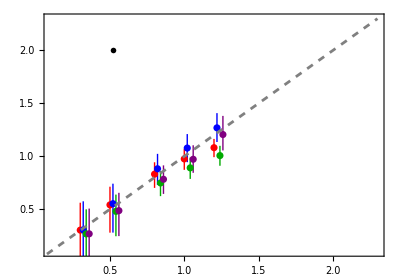

```mathematica
M4TeVPlot = Show[ListPlot[
{
M4TeV["d6"],
M4TeV["d6sq"],
M4TeV["d8"],
M4TeV["d8sq"]
},
Frame->True,
PlotRange -> {{0.1,2.3}, {0.1, 2.3}},
FrameTicks->{{tickWithLabels,tickNoLabels},{tickWithLabels,tickNoLabels}},
AspectRatio-> 0.7,
PlotStyle->{Red,Blue,Darker[Green], Purple},
LabelStyle -> Directive[Black, 20, FontFamily -> "CMU Serif", Thickness[0.001]],
FrameStyle->Directive[Black,Thickness[0.003]],
Epilog-> {Text[MaTeX["M_X = 4 \\, \\text{TeV}", FontSize->18], {0.52, 2}]},
FrameLabel->{
			MaTeX["\\beta_\\text{true}", FontSize->25],
			MaTeX["\\beta_\\text{best-fit}", FontSize->25]
		},
LabelStyle->Directive[Black,5,FontFamily->"CMU Serif"]
],
Plot[x, {x, 0, 2.3}, PlotStyle->{Gray, Dashed}]
]
```

#### MXX = 5 TeV

```mathematica
results5TeV["d6"] = Select[fit["d6"], #[["MXX"]] === 5 &];
```

```mathematica
results5TeV["d6sq"] = Select[fit["d6sq"], #[["MXX"]] === 5 &];
```

```mathematica
results5TeV["d8"] = Select[fit["d8"], #[["MXX"]] === 5 &];
```

```mathematica
results5TeV["d8sq"] = Select[fit["d8sq"], #[["MXX"]] === 5 &];
```

```mathematica
M5TeV["d6"] = {#[["β"]],Around[ #[["βfit"]], ErrorBar[#[["βfit"]], #[["σβ"]]] ]} & /@results5TeV["d6"];
```

```mathematica
M5TeV["d6sq"] = {#[["β"]]+0.02,Around[ #[["βfit"]], ErrorBar[#[["βfit"]], #[["σβ"]]] ]} & /@results5TeV["d6sq"];
```

```mathematica
M5TeV["d8"] = {#[["β"]]+0.04,Around[ #[["βfit"]], ErrorBar[#[["βfit"]], #[["σβ"]]] ]} & /@results5TeV["d8"];
```

```mathematica
M5TeV["d8sq"] = {#[["β"]]+0.06,Around[ #[["βfit"]], ErrorBar[#[["βfit"]], #[["σβ"]]] ]} & /@results5TeV["d8sq"];
```

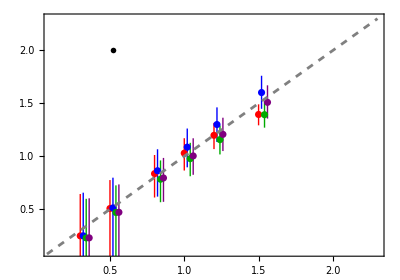

```mathematica
M5TeVPlot = Show[ListPlot[
{
M5TeV["d6"],
M5TeV["d6sq"],
M5TeV["d8"],
M5TeV["d8sq"]
},
Frame->True,
PlotRange -> {{0.1, 2.3}, {0.1,2.3}},
FrameTicks->{{tickWithLabels,tickNoLabels},{tickWithLabels,tickNoLabels}},
AspectRatio-> 0.7,
PlotStyle->{Red,Blue,Darker[Green], Purple},
LabelStyle -> Directive[Black, 20, FontFamily -> "CMU Serif", Thickness[0.001]],
FrameStyle->Directive[Black,Thickness[0.003]],
Epilog-> {Text[MaTeX["M_X = 5 \\, \\text{TeV}", FontSize->18], {0.52, 2}]},
FrameLabel->{
			MaTeX["\\beta_\\text{true}", FontSize->25],
			MaTeX["\\beta_\\text{best-fit}", FontSize->25]
		}
],
Plot[x, {x, 0, 2.3}, PlotStyle->{Gray, Dashed}]
]
```

#### MXX = 6 TeV

```mathematica
results6TeV["d6"] = Select[fit["d6"], #[["MXX"]] === 6 &];
```

```mathematica
results6TeV["d6sq"] = Select[fit["d6sq"], #[["MXX"]] === 6 &];
```

```mathematica
results6TeV["d8"] = Select[fit["d8"], #[["MXX"]] === 6 &];
```

```mathematica
results6TeV["d8sq"] = Select[fit["d8sq"], #[["MXX"]] === 6 &];
```

```mathematica
M6TeV["d6"] = {#[["β"]],Around[ #[["βfit"]], ErrorBar[#[["βfit"]], #[["σβ"]]] ]} & /@results6TeV["d6"];
```

```mathematica
M6TeV["d6sq"] = {#[["β"]]+0.02,Around[ #[["βfit"]], ErrorBar[#[["βfit"]], #[["σβ"]]] ]} & /@results6TeV["d6sq"];
```

```mathematica
M6TeV["d8"] = {#[["β"]]+0.04,Around[ #[["βfit"]], ErrorBar[#[["βfit"]], #[["σβ"]]] ]} & /@results6TeV["d8"];
```

```mathematica
M6TeV["d8sq"] = {#[["β"]]+0.06,Around[ #[["βfit"]], ErrorBar[#[["βfit"]], #[["σβ"]]] ]} & /@results6TeV["d8sq"];
```

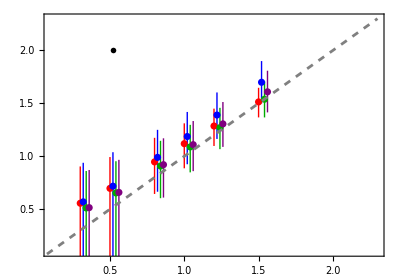

```mathematica
M6TeVPlot = Show[ListPlot[
{
M6TeV["d6"],
M6TeV["d6sq"],
M6TeV["d8"],
M6TeV["d8sq"]
},
Frame->True,
PlotRange -> {{0.1, 2.3}, {0.1, 2.3}},
FrameTicks->{{tickWithLabels,tickNoLabels},{tickWithLabels,tickNoLabels}},
AspectRatio-> 0.7,
PlotStyle->{Red,Blue,Darker[Green], Purple},
LabelStyle -> Directive[Black, 20, FontFamily -> "CMU Serif", Thickness[0.001]],
FrameStyle->Directive[Black,Thickness[0.003]],
Epilog-> {Text[MaTeX["M_X = 6 \\, \\text{TeV}", FontSize->18], {0.52, 2}]},
FrameLabel->{
			MaTeX["\\beta_\\text{true}", FontSize->25],
			MaTeX["\\beta_\\text{best-fit}", FontSize->25]
		}
],
Plot[x, {x, 0, 2.3}, PlotStyle->{Gray, Dashed}]
]
```

#### MXX = 7 TeV

```mathematica
results7TeV["d6"] = Select[fit["d6"], #[["MXX"]] === 7 &];
```

```mathematica
results7TeV["d6sq"] = Select[fit["d6sq"], #[["MXX"]] === 7 &];
```

```mathematica
results7TeV["d8"] = Select[fit["d8"], #[["MXX"]] === 7 &];
```

```mathematica
results7TeV["d8sq"] = Select[fit["d8sq"], #[["MXX"]] === 7 &];
```

```mathematica
M7TeV["d6"] = {#[["β"]],Around[ #[["βfit"]], ErrorBar[#[["βfit"]], #[["σβ"]]] ]} & /@results7TeV["d6"];
```

```mathematica
M7TeV["d6sq"] = {#[["β"]]+0.02,Around[ #[["βfit"]], ErrorBar[#[["βfit"]], #[["σβ"]]] ]} & /@results7TeV["d6sq"];
```

```mathematica
M7TeV["d8"] = {#[["β"]]+0.04,Around[ #[["βfit"]], ErrorBar[#[["βfit"]], #[["σβ"]]] ]} & /@results7TeV["d8"];
```

```mathematica
M7TeV["d8sq"] = {#[["β"]]+0.06,Around[ #[["βfit"]], ErrorBar[#[["βfit"]], #[["σβ"]]] ]} & /@results7TeV["d8sq"];
```

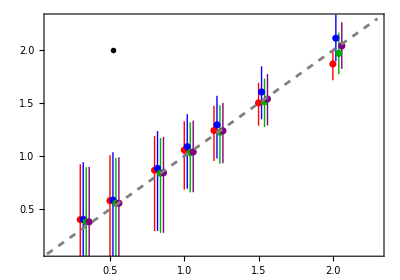

```mathematica
M7TeVPlot = Show[ListPlot[
{
M7TeV["d6"],
M7TeV["d6sq"],
M7TeV["d8"], 
M7TeV["d8sq"]
},
Frame->True,
PlotRange -> {{0.1, 2.3}, {0.1, 2.3}},
FrameTicks->{{tickWithLabels,tickNoLabels},{tickWithLabels,tickNoLabels}},
AspectRatio-> 0.7,
PlotStyle->{Red,Blue,Darker[Green], Purple},
LabelStyle -> Directive[Black, 20, FontFamily -> "CMU Serif", Thickness[0.001]],
FrameStyle->Directive[Black,Thickness[0.003]],
Epilog-> {Text[MaTeX["M_X = 7 \\, \\text{TeV}", FontSize->18], {0.52, 2}]},
FrameLabel->{
			MaTeX["\\beta_\\text{true}", FontSize->25],
			MaTeX["\\beta_\\text{best-fit}", FontSize->25]
		}
],
Plot[x, {x, 0, 2.3}, PlotStyle->{Gray, Dashed}]
]
```

#### MXX = 8 TeV

```mathematica
results8TeV["d6"] = Select[fit["d6"], #[["MXX"]] === 8 &];
```

```mathematica
results8TeV["d6sq"] = Select[fit["d6sq"], #[["MXX"]] === 8 &];
```

```mathematica
results8TeV["d8"] = Select[fit["d8"], #[["MXX"]] === 8 &];
```

```mathematica
results8TeV["d8sq"] = Select[fit["d8sq"], #[["MXX"]] === 8 &];
```

```mathematica
M8TeV["d6"] = {#[["β"]],Around[ #[["βfit"]], ErrorBar[#[["βfit"]], #[["σβ"]]] ]} & /@results8TeV["d6"];
```

```mathematica
M8TeV["d6sq"] = {#[["β"]]+0.02,Around[ #[["βfit"]], ErrorBar[#[["βfit"]], #[["σβ"]]] ]} & /@results8TeV["d6sq"];
```

```mathematica
M8TeV["d8"] = {#[["β"]]+0.04,Around[ #[["βfit"]], ErrorBar[#[["βfit"]], #[["σβ"]]] ]} & /@results8TeV["d8"];
```

```mathematica
M8TeV["d8qsq"] = {#[["β"]]+0.06,Around[ #[["βfit"]], ErrorBar[#[["βfit"]], #[["σβ"]]] ]} & /@results8TeV["d8"];
```

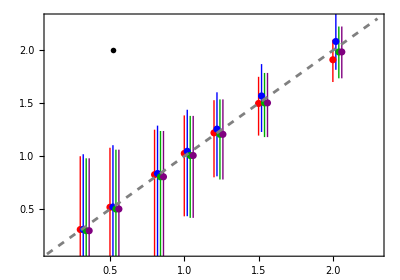

```mathematica
M8TeVPlot = Show[ListPlot[
{
M8TeV["d6"],
M8TeV["d6sq"],
M8TeV["d8"],
M8TeV["d8qsq"]
},
Frame->True,
PlotRange -> {{0.1, 2.3}, {0.1, 2.3}},
FrameTicks->{{tickWithLabels,tickNoLabels},{tickWithLabels,tickNoLabels}},
AspectRatio-> 0.7,
PlotStyle->{Red,Blue,Darker[Green], Purple},
LabelStyle -> Directive[Black, 20, FontFamily -> "CMU Serif", Thickness[0.001]],
FrameStyle->Directive[Black,Thickness[0.003]],

Epilog-> {Text[MaTeX["M_X = 8 \\, \\text{TeV}", FontSize->18], {0.52, 2}]},
FrameLabel->{
			MaTeX["\\beta_\\text{true}", FontSize->25],
			MaTeX["\\beta_\\text{best-fit}", FontSize->25]
		}
],

Plot[x, {x, 0, 2.3}, PlotStyle->{Gray, Dashed}]
]
```

#### Grid plot

```mathematica
legend=SwatchLegend[{Red,Blue,Darker[Green], Purple},{MaTeX["d = 6", FontSize->15],MaTeX["(d = 6)^2", FontSize->15],MaTeX["d = 8", FontSize->15], MaTeX["(d = 8)^2", FontSize->15]},LabelStyle->Directive[Black,4,FontFamily->"CMU Serif"],LegendLayout->"Column"]
```

```mathematica
legendPane=Pane[legend, Alignment->Center, ImageSize->{Automatic,75}  ];
```

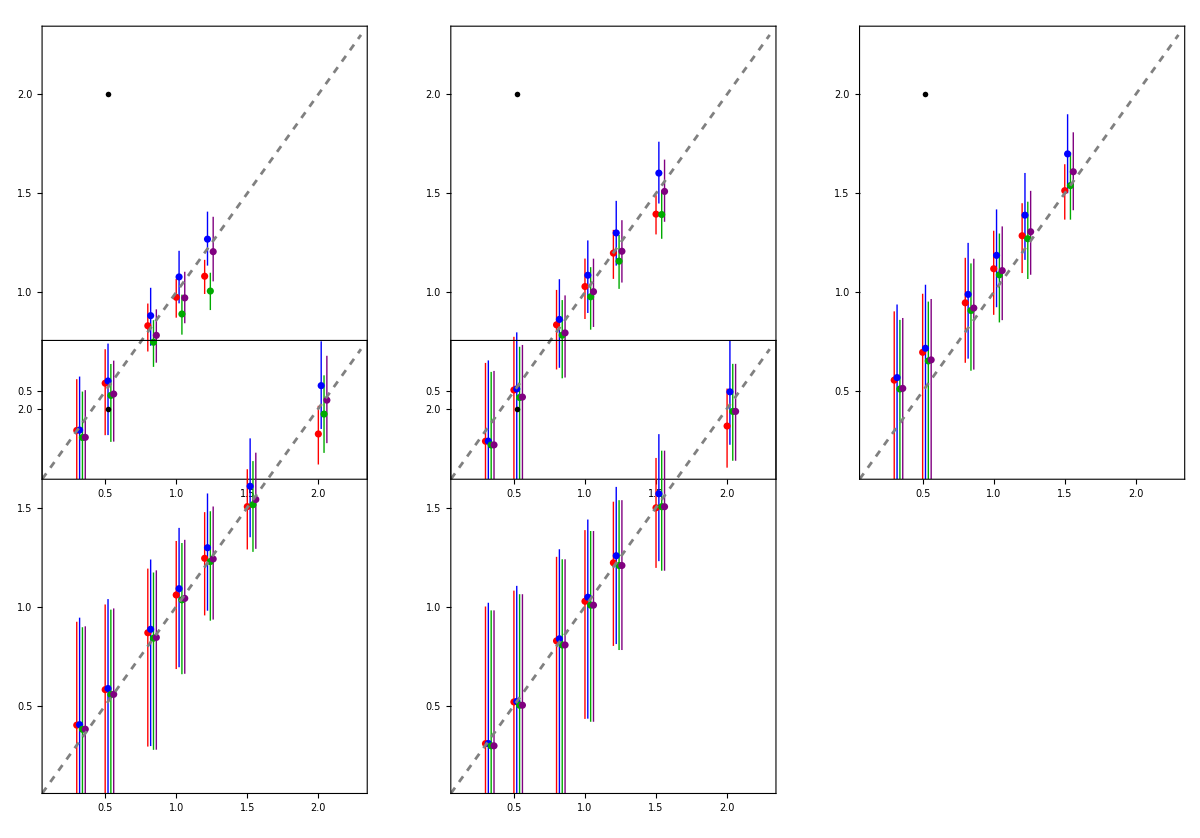

```mathematica
gridplt = GraphicsGrid[
{
{M4TeVPlot, M5TeVPlot, M6TeVPlot},
{M7TeVPlot, M8TeVPlot, legend}
},
Spacings->{5, -40},
ImageSize->1200
]
```

```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
Export["FitZprimeMatching_4F_Clipping_d8sq.pdf", gridplt]
```

FitZprimeMatching_4F_Clipping_d8sq.pdf